```mathematica
$Assumptions=t∈Reals&&t≥0;
```

```mathematica
L=6;
β=0.01;
Subscript[h, 0]=0;
Subscript[h, f]=0.2;
α=0.8;
```

```mathematica
(*Energies*)
ϵ[k_,h_]:=2*Sqrt[Sin[k]^2 + (h-Cos[k])^2]
```

```mathematica
(*Partition function Subscript[Z, 0]*)
Subscript[Z, 0][L_]:=Product[4*Cosh[β*ϵ[Pi*2*m/L,Subscript[h, 0]]/2]^2,{m,0,L/2}]
```

```mathematica
(*Difference between the final and the initial Bogoliubov angles*)
Δ[k_]:=ArcTan[Sin[k]/(Subscript[h, f]-Cos[k])]-ArcTan[Sin[k]/(Subscript[h, 0]-Cos[k])]
```

```mathematica
(*Eigenvalues of ρ(t) and Subscript[ρ, 0].  s=+1 or -1*)
```

```mathematica
λ[k_,s_]:=Cosh[β*ϵ[k,Subscript[h, 0]]]+s*(Sqrt[2]/2)*Sqrt[Cosh[2*β*ϵ[k,Subscript[h, 0]]]-Cos[2*Δ[k]]]
```

```mathematica
(*Coefficients defined when we calculate α powers of 2x2 matrices*)
Subscript[c, 1][k_,α_]:=(λ[k,1]^α-λ[k,-1]^α)/(λ[k,1]-λ[k,-1])
Subscript[c, 2][k_,α_]:=λ[k,1]*λ[k,-1]*(λ[k,1]^(α-1)-λ[k,-1]^(α-1))/(λ[k,1]-λ[k,-1])
```

```mathematica
(* Subscript[ρ, k^0](1-α) *)
rho0[k_,α_] := {{Subscript[c, 1][k,1-α]*(Exp[-β*ϵ[k,Subscript[h, 0]]]*Cos[Δ[k]/2]^2 + Exp[β*ϵ[k,Subscript[h, 0]]]*Sin[Δ[k]/2]^2)-Subscript[c, 2][k,1-α],Subscript[c, 1][k,1-α]*2*I*Cosh[β*ϵ[k,Subscript[h, 0]]]*Cos[Δ[k]/2]*Sin[Δ[k]/2],0,0},{-Subscript[c, 1][k,1-α]*2*I*Cosh[β*ϵ[k,Subscript[h, 0]]]*Cos[Δ[k]/2]*Sin[Δ[k]/2],Subscript[c, 1][k,1-α]*(Exp[β*ϵ[k,Subscript[h, 0]]]*Cos[Δ[k]/2]^2 + Exp[-β*ϵ[k,Subscript[h, 0]]]*Sin[Δ[k]/2]^2)-Subscript[c, 2][k,1-α],0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
(* rho_k(t,α) *)
rhot[k_,t_,α_] := {{Subscript[c, 1][k,α]*(Exp[-β*ϵ[k,Subscript[h, 0]]]*Cos[Δ[k]/2]^2 + Exp[-β*ϵ[k,Subscript[h, 0]]]*Sin[Δ[k]/2]^2)-Subscript[c, 2][k,α],Subscript[c, 1][k,α]*2*I*Exp[2*I*t*ϵ[k,Subscript[h, f]]]*Cosh[β*ϵ[k,Subscript[h, 0]]]*Cos[Δ[k]/2]*Sin[Δ[k]/2],0,0},{-Subscript[c, 1][k,α]*2*I*Exp[2*I*t*ϵ[k,Subscript[h, f]]]*Cosh[β*ϵ[k,Subscript[h, 0]]]*Cos[Δ[k]/2]*Sin[Δ[k]/2],Subscript[c, 1][k,α]*(Exp[β*ϵ[k,Subscript[h, 0]]]*Cos[Δ[k]/2]^2 + Exp[-β*ϵ[k,Subscript[h, 0]]]*Sin[Δ[k]/2]^2)-Subscript[c, 2][k,α],0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
(*Renyi relative entropy*)
R[α_,t_]:=(1/(α-1))*Log[Re[Tr[(1/Subscript[Z, 0][L])*(Dot@@Table[rhot[Pi*2*m/L,t,α],{m,0,L/2}]).(Dot@@Table[rho0[Pi*2*m/L,α],{m,0,L/2}])]]]
```

```mathematica
(*Plot[Evaluate[Table[R[α,t],{α,{0.2,0.4,0.6,0.8}}]],{t,0,30},PlotLabels->{α=0.2,α=0.4,α=0.6,α=0.8}]*)
```

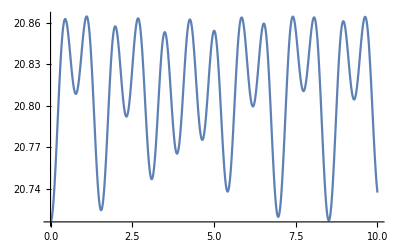

```mathematica
(*Renyi relative entropy*)
Plot[R[α,t],{t,0,10}]
```